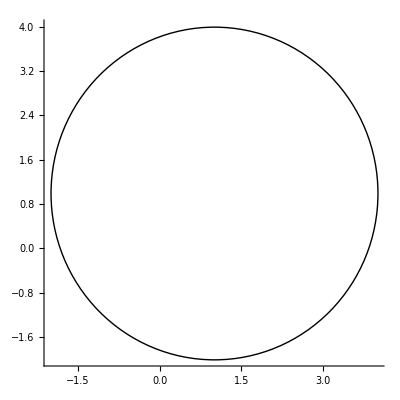

```mathematica
Graphics[Circle[{1,1},3],Axes->True,ImageSize->Tiny]
```

```mathematica
Graphics3D[Sphere[{1,1,1},2],Axes->True,ImageSize->Tiny]
```

-Graphics3D-

```mathematica
Graphics3D[Cuboid[{1,1,1}],Axes->True,ImageSize->Tiny]
```

-Graphics3D-

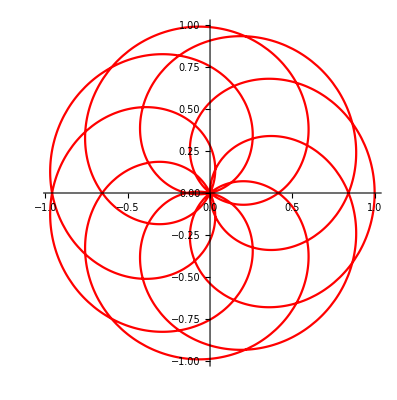

```mathematica
x1[t_]:=Cos[7t]Cos[11t]
y1[t_]:=Cos[7t]Sin[11t]
p1[t_]:={x1[t],y1[t]}
plotg1=ParametricPlot[p1[t],{t,0,Pi},PlotStyle->Red]
```

```mathematica
plot1[s_]:=ParametricPlot[p1[t],{t,0,s},PlotStyle->Red,PlotRange->{{-1,1},{-1,1}},PlotPoints->100]
Manipulate[plot1[s],{s,0.1,Pi,0.001}]
```

```mathematica
Rss:=0.15
```

```mathematica
plot2[s_]:=Graphics[Circle[p1[s],Rss],PlotRange->{{-1,1},{-1,1}},Axes->True]
Manipulate[plot2[s],{s,0.1,Pi,0.001}]
```

```mathematica
plot1and2[s_]:=Show[plot2[s],plotg1]
```

```mathematica
Manipulate[plot1and2[s],{s,0.1,Pi,0.001}]
```

```mathematica
data3={{1,1},{2,3},{2,4},{7,7},{7,5},{7,3},{7,-1},{5,-1}}
```

{{1,1},{2,3},{2,4},{7,7},{7,5},{7,3},{7,-1},{5,-1}}

```mathematica
x3 = Transpose[data3][[1]]
```

{1,2,2,7,7,7,7,5}

```mathematica
y3=Transpose[data3][[2]]
```

{1,3,4,7,5,3,-1,-1}

```mathematica
sx3=Interpolation[x3]
```

InterpolatingFunction[…]

```mathematica
sy3=Interpolation[y3]
```

InterpolatingFunction[…]

```mathematica
s3[t_]:={sx3[t],sy3[t]}
```

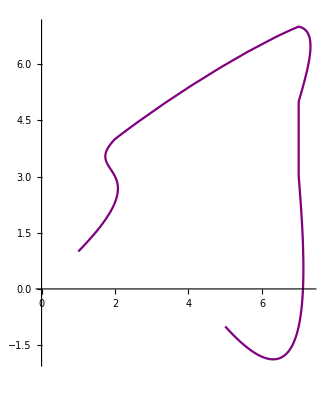

```mathematica
plot31=ParametricPlot[s3[t],{t,1,Length[x3]},PlotStyle->Purple]
```

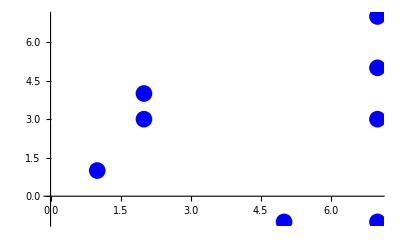

```mathematica
plot32=ListPlot[data3,PlotStyle->{PointSize[0.03],Blue}]
```

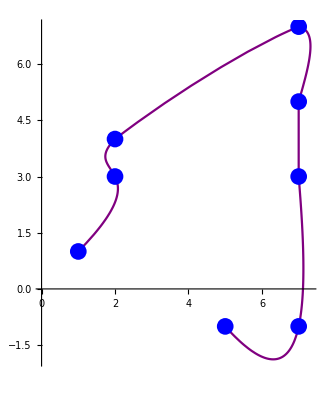

```mathematica
Show[plot31,plot32]
```

```mathematica
Rs4=1.0
```

1.

```mathematica
plot4[s_]:=Graphics[Circle[s3[s],Rs4],PlotRange->{{0,8},{-2,8}},Axes->True]
```

```mathematica
plot3and4[s_]:=Show[plot4[s],plot31]
```

```mathematica
Manipulate[plot3and4[s],{s,1,Length[x3]}]
```

```mathematica
data5={{1,1,1},{2,3,1},{1,3,2},{4,3,3},{4,4,4},{5,3,2},{7,5,6},{5,5,5}}
```

{{1,1,1},{2,3,1},{1,3,2},{4,3,3},{4,4,4},{5,3,2},{7,5,6},{5,5,5}}

```mathematica
x5=Transpose[data5][[1]]
```

{1,2,1,4,4,5,7,5}

```mathematica
y5=Transpose[data5][[2]]
```

{1,3,3,3,4,3,5,5}

```mathematica
z5=Transpose[data5][[3]]
```

{1,1,2,3,4,2,6,5}

```mathematica
sx5=Interpolation[x5]
```

InterpolatingFunction[…]

```mathematica
sy5=Interpolation[y5]
```

InterpolatingFunction[…]

```mathematica
sz5=Interpolation[z5]
```

InterpolatingFunction[…]

```mathematica
s5[t_]:={sx5[t],sy5[t],sz5[t]}
```

```mathematica
plot51=ListPointPlot3D[data5,PlotStyle->PointSize[0.05]]
```

-Graphics3D-

```mathematica
plot52=ParametricPlot3D[s5[t],{t,1,Length[x5]},PlotStyle->{Red,Thick}]
```

-Graphics3D-

```mathematica
Show[plot52,plot51]
```

-Graphics3D-

```mathematica
plotg6[s_]:=ParametricPlot3D[s5[t],{t,1,s},PlotStyle->{Red,Thick},PlotRange->{{0,8},{0,8},{0,7}}]
```

```mathematica
plot6show[s_]:=Show[plotg6[s],plot51]
```

```mathematica
Manipulate[plot6show[s],{s,1.1,Length[x5]}]
```

```mathematica
Rs6=0.8
```

0.8

```mathematica
plotc7[t_]:=Graphics3D[Sphere[s5[t],Rs6],PlotRange->{{0,8},{0,8},{0,7}}]
```

```mathematica
plot7show[s_]:=Show[plotc7[s],plot52,plot51]
```

```mathematica
Manipulate[plot7show[s],{s,1.1,Length[x5]}]
```

```mathematica
smax=20
```

20

```mathematica
Rs8=0.5
```

0.5

```mathematica
R8=1.5
```

1.5

```mathematica
x8[t_]:=R8*Cos[t]
```

```mathematica
y8[t_]:=R8*Sin[t/1.2]
```

```mathematica
z8[t_]:=t/5
```

```mathematica
s8[t_]:={x8[t],y8[t],z8[t]}
```

```mathematica
plot81=ParametricPlot3D[s8[t],{t,0,smax}]
```

-Graphics3D-

```mathematica
plotc888[t_]:=Graphics3D[Sphere[s8[t],Rs8],PlotRange->{{0,8},{0,8},{0,7}}]
```

```mathematica
plot8show[s_]:=Show[plot81,plotc888[s]]
```

```mathematica
Manipulate[plot8show[s],{s,0,smax}]
```

```mathematica
Graphics3D[Cuboid[{0,0,1}],ImageSize->Tiny,Axes->True]
```

-Graphics3D-

```mathematica
data9={{0,0,0},{1,1,1},{0,0,3},{1,1,2},{1,1,3},{2,1,1},{2,2,2}}
```

{{0,0,0},{1,1,1},{0,0,3},{1,1,2},{1,1,3},{2,1,1},{2,2,2}}

```mathematica
x9=Transpose[data9][[1]]
```

{0,1,0,1,1,2,2}

```mathematica
y9=Transpose[data9][[2]]
```

{0,1,0,1,1,1,2}

```mathematica
z9=Transpose[data9][[3]]
```

{0,1,3,2,3,1,2}

```mathematica
sx9=Interpolation[x9]
```

InterpolatingFunction[…]

```mathematica
sy9=Interpolation[y9]
```

InterpolatingFunction[…]

```mathematica
sz9=Interpolation[z9]
```

InterpolatingFunction[…]

```mathematica
s9[t_]:={sx9[t],sy9[t],sz9[t]}
```

```mathematica
plot91=ListPointPlot3D[data9,PlotStyle->PointSize[0.05]]
```

-Graphics3D-

```mathematica
plot92=ParametricPlot3D[s9[t],{t,1,Length[x9]},PlotStyle->Red]
```

-Graphics3D-

```mathematica
Show[plot92,plot91]
```

-Graphics3D-

```mathematica
plotc9[t_]:=Graphics3D[Cuboid[s9[t]],ImageSize->Tiny,Axes->True]
```

```mathematica
plot9show[s_]:=Show[plot92,plot91,plotc9[s]]
```

```mathematica
Manipulate[plot9show[s],{s,1,Length[x9]}]
```

```mathematica
x10[t_]:=0.1*Sin[t]
```

```mathematica
y10[t_]:=0.3*Cos[t]
```

```mathematica
RM[a_]:=RotationMatrix[a]
```

```mathematica
s10[t_]:={x10[t],y10[t]}
```

```mathematica
srotated10[t_]:=RM[45*Degree].s10[t]
```

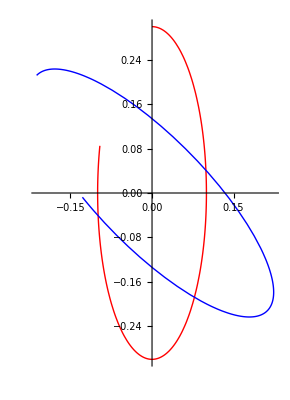

```mathematica
ParametricPlot[{s10[t],srotated10[t]},{t,0,5},PlotStyle->{{Red,Thick},{Blue,Thick}}]
```

```mathematica
srotated11[t_,a_]:=RM[a].s10[t]
plotg11[a_]:=ParametricPlot[srotated11[t,a],{t,0,5},PlotStyle->{{Red,Thick},{Blue,Thick}},PlotRange->{{-0.5,0.5},{-0.5,0.5}}]
```

```mathematica
Manipulate[plotg11[a],{a,0,360*Degree,1*Degree}]
```

```mathematica
data12={{1,1},{2,3},{2,4},{7,7},{7,5},{7,3},{7,-1},{5,-1}}
```

{{1,1},{2,3},{2,4},{7,7},{7,5},{7,3},{7,-1},{5,-1}}

```mathematica
x12=Transpose[data12][[1]]
```

{1,2,2,7,7,7,7,5}

```mathematica
y12=Transpose[data12][[2]]
```

{1,3,4,7,5,3,-1,-1}

```mathematica
sx12=Interpolation[x12]
```

InterpolatingFunction[…]

```mathematica
sy12=Interpolation[y12]
```

InterpolatingFunction[…]

```mathematica
s12[t_]:={sx12[t],sy12[t]}
```

```mathematica
RM12[a12_]:=RotationMatrix[a12]
```

```mathematica
s12rotated[t_,a_]:=RM12[a].s12[t]
```

```mathematica
plot12[a_]:=ParametricPlot[{s12[t],s12rotated[t,a]},{t,1,Length[x12]},PlotStyle->{{Red,Thick}},PlotRange->{{-10,10},{-10,10}}]
```

```mathematica
Manipulate[plot12[a],{a,0,360*Degree,1*Degree}]
```

```mathematica
Paround={1,0.5}
```

{1,0.5}

```mathematica
srotated13[t_,a_]:=RM[a].(s10[t]-Paround)+Paround
```

```mathematica
plotg13[a_]:=ParametricPlot[srotated13[t,a],{t,0,5},PlotStyle->{{Red,Thick}},PlotRange->{{-3,3},{-1,2}}]
```

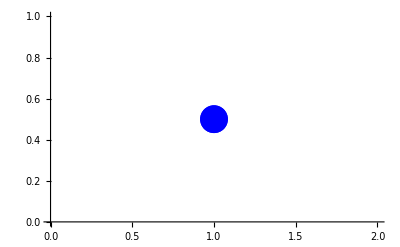

```mathematica
plot113=ListPlot[{Paround},PlotStyle->{Blue,PointSize[0.05]}]
```

```mathematica
plotg13show[a_]:=Show[{plotg13[a],plot113}]
```

```mathematica
Manipulate[plotg13show[a],{a,0,360*Degree,1*Degree}]
```

```mathematica
Paround14={1,1.5}
```

{1,1.5}

```mathematica
s14rotated[t_,a_]:=RM[a].(s12[t]-Paround)+Paround
```

```mathematica
plotg14[a_]:=ParametricPlot[s14rotated[t,a],{t,0,5},PlotStyle->{{Red,Thick}},PlotRange->{{-3,3},{-1,2}}]
```

```mathematica
plot114=ListPlot[{Paround},PlotStyle->{Blue,PointSize[0.05]}]
```

-Graphics-